### Dependency highlight

```mathematica
all = Join[Sequence@@Values[$LifeParts]];
```

```mathematica
mat=Boole[Outer[SubsetQ[#2,#1]&,
Values[all],
Values[all],
1]];
```

```mathematica
overlap = Select[Position[mat, 1], #[[1]] != #[[2]]&];
```

```mathematica
names = Map[Keys[all][[#]]&, overlap, {2}];
```

```mathematica
Iconize[names]
```

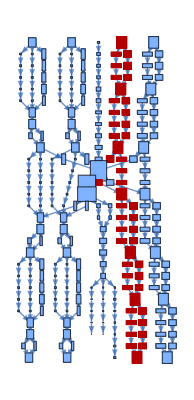

```mathematica
HighlightGraph[#[[2]], 
VertexList[#[[2]]][[
(Function[{left, right},With[{common=Intersection[left,right]},{Flatten[Position[left,#]&/@common],Flatten[Position[right,#]&/@common]}]]@@
(Map[
(SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&), 
VertexList/@ #, {2}]))[[2]]]]]&/@ Map[BoundingBoxLayeredGraph[$LifeData[#]]&, names[[{1}]], {2}]
```

```mathematica
HighlightGraph[#[[2]], 
VertexList[#[[2]]][[
(Function[{left, right},With[{common=Intersection[left,right]},{Flatten[Position[left,#]&/@common],Flatten[Position[right,#]&/@common]}]]@@
(Map[
(SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&), 
VertexList/@ #, {2}]))[[2]]]]]&/@ Map[BoundingBoxLayeredGraph[$LifeData[#]]&, names[[{1}]], {2}]
```

{-Graphics-}

### Figuring out what’s wrong with year plot

```mathematica
years = Reverse/@Map[$LifeData[#]["Year"]&, names, {2}];
```

```mathematica
d = Map[$LifeData, names, {2}];
```

```mathematica
ds = Map[#[[{"Name", "Year"}]]&,Select[d, #[[1, "Year"]]>#[[2, "Year"]]&], {2}];
```

```mathematica
ds[[1, All, "Name"]]
```

{34P7,p182pihassler}

```mathematica
ds
```

{{<|Name→34P7,Year→2022|>,<|Name→p182pihassler,Year→2021|>},{<|Name→64P6,Year→2019|>,<|Name→p12rpentominohasslers,Year→1995|>},{<|Name→Karel's p15,Year→2002|>,<|Name→p60 traffic light hassler,Year→1995|>},{<|Name→Monogram,Year→1989|>,<|Name→Carnival shuttle,Year→1984|>},{<|Name→Odd traffic stop,Year→2023|>,<|Name→p55piheptominohassler2,Year→2014|>},{<|Name→p58 pre-pulsar shuttle,Year→2015|>,<|Name→p55prepulsarshuttle,Year→2012|>},{<|Name→p6 thumb,Year→2000|>,<|Name→p12rpentominohasslers,Year→1995|>},{<|Name→p6 thumb,Year→2000|>,<|Name→Period-246 glider gun,Year→1996|>},{<|Name→Block on table,Year→1972|>,<|Name→Noah's ark,Year→1971|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→106P135,Year→1989|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→Crystallization and decay oscillator,Year→1990|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→p120-based PRNG,Year→1992|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→Gosper glider gun,Year→1970|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→Gunstar,Year→1990|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→Gunstar 2,Year→1991|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→New gun 1,Year→1971|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→P94S,Year→1990|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→Period-60 glider gun,Year→1970|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→Period-808 glider gun,Year→1991|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→Period-856 glider gun,Year→1991|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→Glider-producing switch engine,Year→1971|>},{<|Name→Three-block shifter,Year→1994|>,<|Name→Noah's ark,Year→1971|>},{<|Name→Silver's reflector,Year→1998|>,<|Name→Crystallization and decay oscillator,Year→1990|>},{<|Name→Silver's reflector,Year→1998|>,<|Name→p120-based PRNG,Year→1992|>},{<|Name→Silver's reflector,Year→1998|>,<|Name→Gunstar,Year→1990|>},{<|Name→Silver's reflector,Year→1998|>,<|Name→Gunstar 2,Year→1991|>},{<|Name→Silver's reflector,Year→1998|>,<|Name→P94S,Year→1990|>},{<|Name→Silver's reflector,Year→1998|>,<|Name→Period-690 glider gun,Year→1996|>},{<|Name→Silver's reflector,Year→1998|>,<|Name→Period-808 glider gun,Year→1991|>},{<|Name→Silver's reflector,Year→1998|>,<|Name→Period-856 glider gun,Year→1991|>},{<|Name→CC semi-Snark,Year→2013|>,<|Name→Crystallization and decay oscillator,Year→1990|>},{<|Name→CC semi-Snark,Year→2013|>,<|Name→Gunstar,Year→1990|>},{<|Name→CC semi-Snark,Year→2013|>,<|Name→Gunstar 2,Year→1991|>},{<|Name→CC semi-Snark,Year→2013|>,<|Name→Period-856 glider gun,Year→1991|>},{<|Name→CC semi-Snark,Year→2013|>,<|Name→487-tick reflector,Year→2009|>},{<|Name→p8 bumper,Year→2016|>,<|Name→Gunstar 2,Year→1991|>},{<|Name→p8 bumper,Year→2016|>,<|Name→Period-808 glider gun,Year→1991|>},{<|Name→p8 bumper,Year→2016|>,<|Name→Period-856 glider gun,Year→1991|>}}

```mathematica
Dataset[ds[[All, 1]]]
```

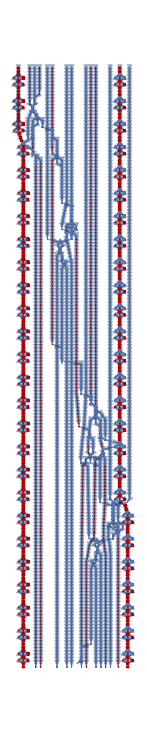

```mathematica
HighlightGraph[#[[2]], 
VertexList[#[[2]]][[
(Function[{left, right},With[{common=Intersection[left,right]},{Flatten[Position[left,#]&/@common],Flatten[Position[right,#]&/@common]}]]@@
(Map[
(SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&), 
VertexList/@ #, {2}]))[[2]]]]]&/@ Map[BoundingBoxLayeredGraph[$LifeData[#]]&, {ds[[1, All, "Name"]]}, {2}]
```

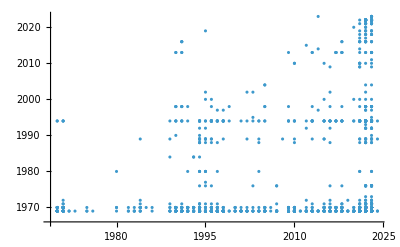

```mathematica
ListPlot[years]
```

```mathematica
sas = Map[
(SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&), 
VertexList/@ #, {2}]&/@Map[BoundingBoxLayeredGraph[$LifeData[#]]&, {ds[[1, All, "Name"]]}, {2}];
```

```mathematica
ArrayPlot/@(Intersection@@sas[[1]])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Showing that they do indeed have overlaps in our data^

```mathematica
pes = PatternElements[$LifeData[#]["MatrixData"]]&@ds[[1, 2, "Name"]];
```


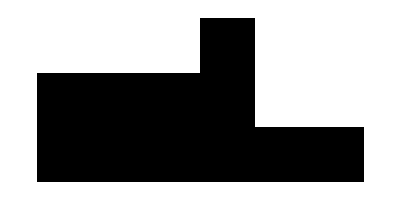
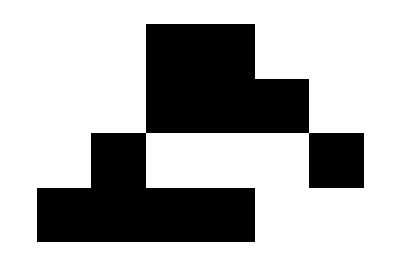
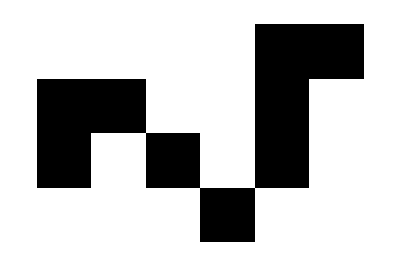
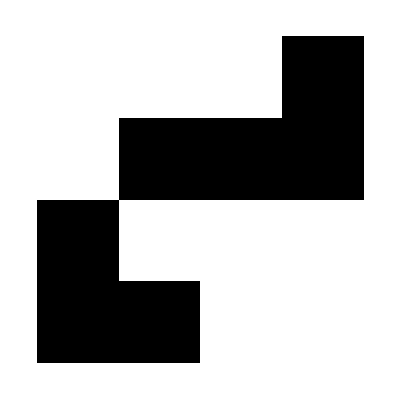
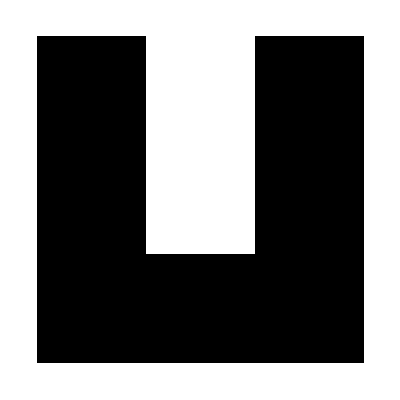
<|-Graphics-→5,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→1|>

```mathematica
KeyMap[ArrayPlot, pes]
```

```mathematica
als = AllLifeElements[$LifeData[#]["MatrixData"], $LifeData[#]["Period"]]&/@ ds[[1, All, "Name"]];
```

```mathematica
ArrayPlot/@ als[[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

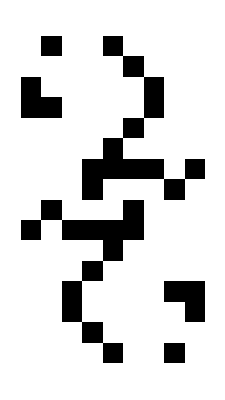
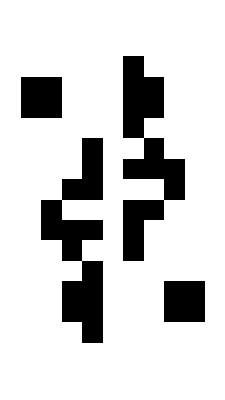
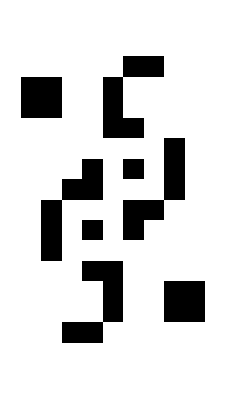
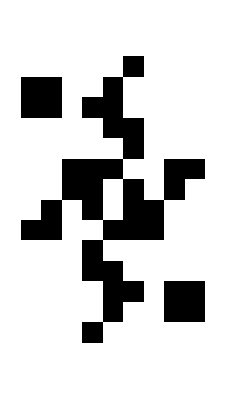
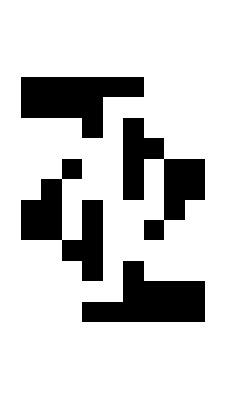
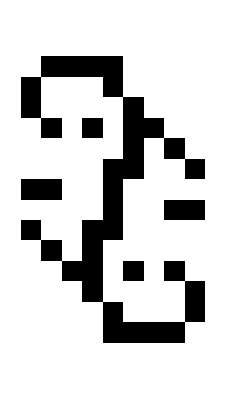
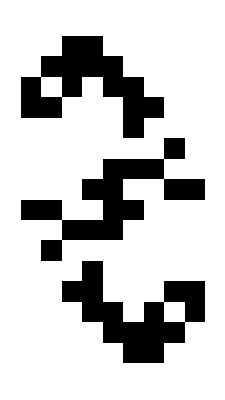
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
(ArrayPlot/@CellularAutomaton["GameOfLife", {$LifeData[#]["MatrixData"], 0}, 10])&/@ds[[1, All, "Name"]]
```

#### V2

```mathematica
ds[[1, All, "Name"]]
```

{34P7,p182pihassler}

#### V3

```mathematica
ds[[]]
```

### V3

```mathematica
names = ;
```

```mathematica
{"34P7","p182pihassler"}
```

```mathematica
$LifeData["34P7"]["Year"]
```

2022

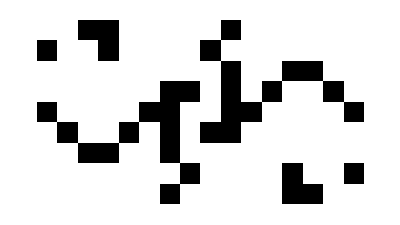
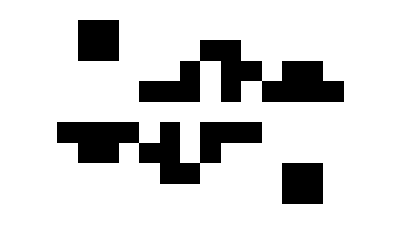
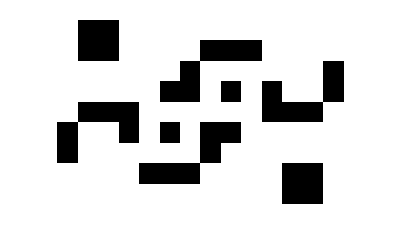
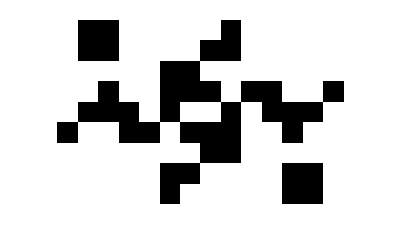
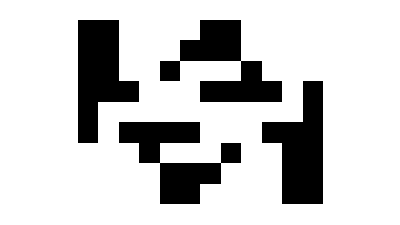
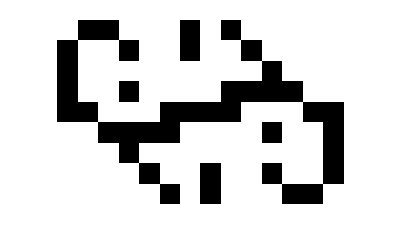
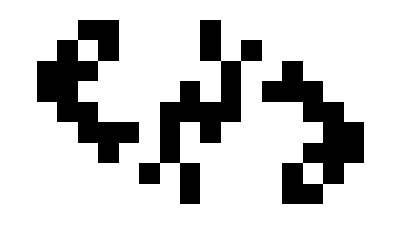
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@CellularAutomaton["GameOfLife", {ResourceFunction["ArrayRotations"][$LifeData["34P7"]["MatrixData"]][[5]], 0}, $LifeData["34P7"]["Period"]]
```

```mathematica
$LifeData["p182pihassler"]["Year"]
```

2021

```mathematica
ArrayPlot[#,Mesh->False, MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife", {PatternCanonicalize[$LifeData["p182pihassler"]["MatrixData"]], 0}, {{3, 10}, {0, 8},{-2, 13}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[#,Mesh->False, MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife", {PatternCanonicalize[$LifeData["p182pihassler"]["MatrixData"]], 0}, {{3, 10}, {0, 8},{-2, 13}}] ===ArrayPlot/@CellularAutomaton["GameOfLife", {ResourceFunction["ArrayRotations"][$LifeData["34P7"]["MatrixData"]][[5]], 0}, $LifeData["34P7"]["Period"]]
```

True

Regular:

```mathematica
ArrayPlot[#,Mesh->False, MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife", {PatternCanonicalize[$LifeData["p182pihassler"]["MatrixData"]], 0}, {{3, 10}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

We need to ask Ed about something like this

So basically, what happened is that it was updated in 2023, to use the  new oscillator

### V4

```mathematica
ds[[2, All, {"Name", "Year"}]]
```

{<|Name→64P6,Year→2019|>,<|Name→p12rpentominohasslers,Year→1995|>}

```mathematica
ds[[3, All, {"Name", "Year"}]]
```

{<|Name→Karel's p15,Year→2002|>,<|Name→p60 traffic light hassler,Year→1995|>}

Yep so this one above was an improvement as well^ guessing they’re all improvements